#### CALCULATION WITH NO CONTROL (ALLOWED FREQUENCY)

```mathematica
tend=600;Xend=180; a=0.5;bet1=0.1; bet2=0.05;om=0.5;B=0.25;range=Xend;nonlin1=0;Xinterest=60;Tend=tend;
```

Amplitude ratio

```mathematica
rat = (bet1 - om^2)/bet1
```

-1.5

Band gap

```mathematica
Sqrt[bet1]
```

0.316228

```mathematica
Sqrt[bet1+bet2]
```

0.387298

```mathematica
λ=0.03;eps=0.00001;(*epsilon должен быть ненулевым, чтобы математика не ругалась на минус бесконечность при численном решении*)
mask=Tanh[λ(range*(1+eps)-x)]^2;
```

```mathematica
fmask=Log[mask];(*данная функция должна быть очень близка у нулю в области моделирования и убывать на минус бесконечность ближе к границам области. можно использовать любую, это первая удачная*)
```

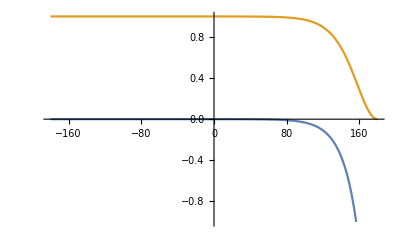

```mathematica
Plot[{fmask,mask},{x,-range,range},PlotRange->{-1,1}]
```

```mathematica
u0=0.5*Exp[-((x))^2];
```

One can include the logarithm of the masking function to the partial differential equation

```mathematica
eqnOrig=D[uR[t,x],t]==a^2 D[u[t,x],{x,2}]+bet2(v[t,x]-u[t,x])+nonlin1 (v[t,x]-u[t,x])^2;
eqnLog=D[u[t,x],t]==uR[t,x]+fmask u[t,x];(*в области где fmask=0, система сводится к волновому уравнению*)
```

```mathematica
eq2=D[v[t,x],t,t]==-bet1(v[t,x]-u[t,x])+nonlin1 (v[t,x]-u[t,x])^2;
```

```mathematica
ic={(u[t,x]/.t->0)==0,(uR[t,x]/.t->0)== 0,(v[t,x]/.t->0)== 0,(D[v[t,x],t]/.t->0)== 0};
bc={(uR[t,x]/.x->-range)==0.25 rat om Cos[om t],(u[t,x]/.x->-range)==B rat Sin[om t],(v[t,x]/.x->-range)==B Sin[om t]};(*это условние необходимо поставить, т.к. уравнение все равно второго порядка, но оно минимально влияет на решение*)
```

```mathematica
uRsol=NDSolve[{eqnOrig,eqnLog,eq2,ic,bc},{u,uR,v},{t,0,tend},{x,-range,range},Method->{"MethodOfLines","SpatialDiscretization" -> {"FiniteElement",  "MeshOptions" -> {"MaxCellMeasure" ->2}}}]
```

{{u→InterpolatingFunction[{{0., 600.}, {-180., 180.}}, <>],uR→InterpolatingFunction[{{0., 600.}, {-180., 180.}}, <>],v→InterpolatingFunction[{{0., 600.}, {-180., 180.}}, <>]}}

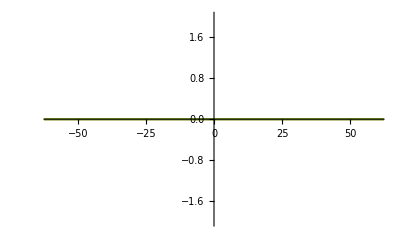

```mathematica
Plot[{Evaluate[u[t,x]/.uRsol/.t->0],Evaluate[u[t,x]/.uRsol/.t->1],Evaluate[u[t,x]/.uRsol/.t->2]},{x,-range,range},PlotRange->{{-Xinterest,Xinterest},{-2,2}}]
```

#### PLOTS FOR CALCULATION WITH NO CONTROL

```mathematica
Prange={-0.5,0.5};
```

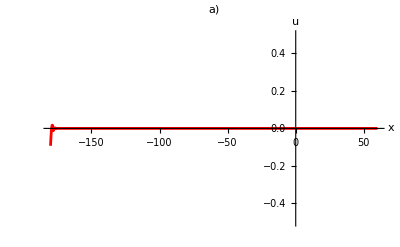

```mathematica
P1=Plot[Evaluate[u[t,x]/.uRsol/.t->0.5],{x,-range,Xinterest}, PlotStyle->{Thickness[0.005],Red},AxesLabel->{"x","u"},PlotRange->Prange,LabelStyle->Directive[Black,Italic,15], PlotLabel->"        a)"]
```

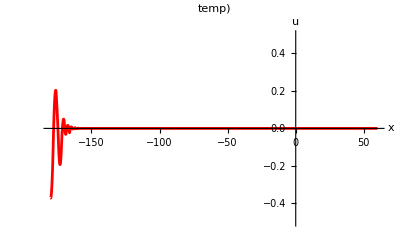

```mathematica
Pt=Plot[Evaluate[u[t,x]/.uRsol/.t->16],{x,-range,Xinterest}, PlotStyle->{Thickness[0.005],Red},AxesLabel->{"x","u"},PlotRange->Prange,LabelStyle->Directive[Black,Italic,15], PlotLabel->"        temp)"]
```

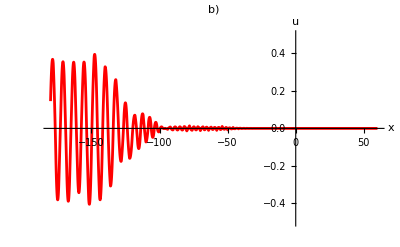

```mathematica
P2=Plot[Evaluate[u[t,x]/.uRsol/.t->Tend/4],{x,-range,Xinterest},PlotRange-> Prange, PlotStyle->{Thickness[0.005],Red},AxesLabel->{"x","u"},LabelStyle->Directive[Black,Italic,15], PlotLabel->"        b)"]
```

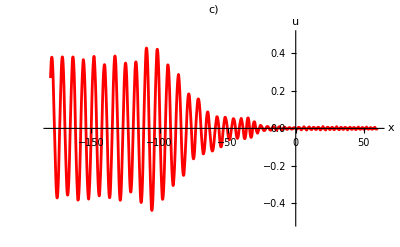

```mathematica
P3=Plot[Evaluate[u[t,x]/.uRsol/.t->Tend/2],{x,-range,Xinterest},PlotRange-> Prange, PlotStyle->{Thickness[0.005],Red},AxesLabel->{"x","u"},LabelStyle->Directive[Black,Italic,15], PlotLabel->"        c)"]
```

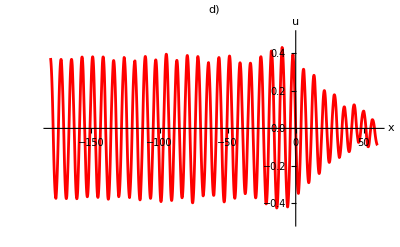

```mathematica
P4=Plot[Evaluate[u[t,x]/.uRsol/.t->Tend],{x,-range,Xinterest},PlotRange-> Prange, PlotStyle->{Thickness[0.005],Red},AxesLabel->{"x","u"},LabelStyle->Directive[Black,Italic,15], PlotLabel->"        d)"]
```

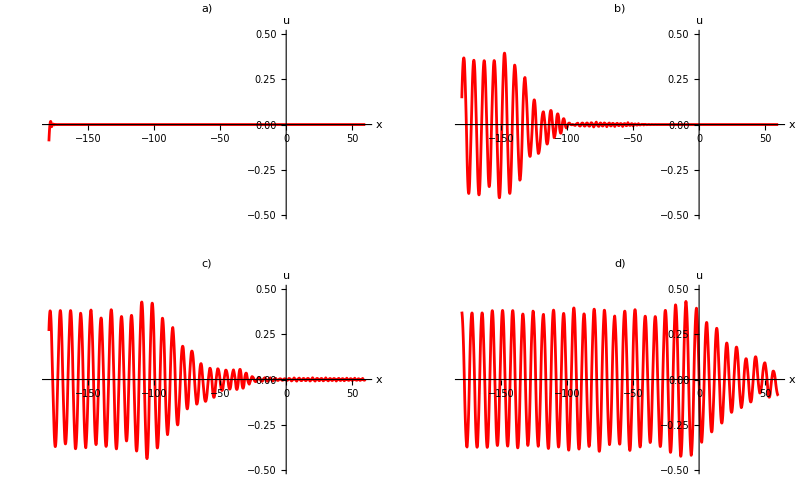

```mathematica
Show[GraphicsGrid[{{P1,P2},{P3,P4}}],LabelStyle->Directive[Black,Italic,15]]
```

#### Spectrogram

```mathematica
toSpectre=Evaluate[First[u[t,x]/.uRsol]]/.x->-50;
```

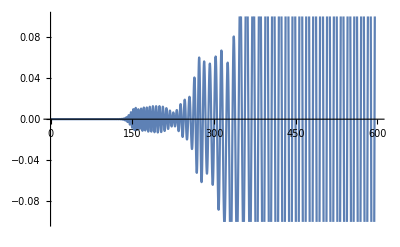

```mathematica
plotToSpectre=Plot[toSpectre,{t,0,tend},PlotRange->{-0.1,0.1}]
```

```mathematica
frate=0.5;
```

```mathematica
data=Table[toSpectre,{t,0,tend,1*frate}];
```

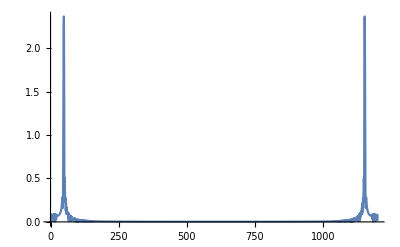

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
Options[Domains]={DeltaT->None,TotalT->None,DeltaF->None,TotalF->None,Toffset->0,Centered->False,OnlyParameters->False};

Domains[n_,opts___]:=Module[{tos,Ts,Ttot,Fs,Ftot,centered,param,timedomain,frequencydomain},Ts=DeltaT/.{opts}/.Options[Domains];
Ttot=TotalT/.{opts}/.Options[Domains];
Fs=DeltaF/.{opts}/.Options[Domains];
Ftot=TotalF/.{opts}/.Options[Domains];
tos=Toffset/.{opts}/.Options[Domains];
centered=Centered/.{opts}/.Options[Domains];
param=OnlyParameters/.{opts}/.Options[Domains];
Switch[First[Flatten[Position[N[{Ts,Ttot,Fs,Ftot,tos}],_?NumberQ]]],1,Ttot=n Ts;Fs=1/Ttot;Ftot=1/Ts,2,Ts=Ttot/n;Fs=1/Ttot;Ftot=1/Ts,3,Ts=1/(n Fs);Ttot=1/Fs;Ftot=n Fs,4,Ts=1/Ftot;Ttot=n Ts;Fs=Ftot/n,_,Ts=1;Ttot=n;Fs=1/n;Ftot=1];
If[param,Return[{Ts,Ttot,Fs,Ftot}],timedomain=tos+(Range[n]-1)Ts;
frequencydomain=If[centered,(Range[n]-Ceiling[n/2])Fs,(Range[n]-1)Fs];
Return[{timedomain,frequencydomain}]]]

Options[AddSignalRange]={Toffset->0};

AddSignalRange[data_List,opts___]:=Transpose[{Domains[Length[data],opts][[1]],data}]

Options[AddSpectrumRange]={Centered->False,HalfSpectrum->False};

AddSpectrumRange[data_List,opts___]:=Module[{n,lista,half,centered},half=HalfSpectrum/.{opts}/.Options[AddSpectrumRange];
If[half,centered=False,centered=Centered/.{opts}/.Options[AddSpectrumRange];];
n=Length[data];
lista=If[centered,Transpose[{Domains[n,Centered->True,opts][[2]],RotateRight[data,Ceiling[n/2]-1]}],Transpose[{Domains[n,Centered->False,opts][[2]],data}]];
If[half,(*then centered is forced to False*)Take[lista,{1,Ceiling[(n+1)/2]}],lista (*can be centered or not*)]]
```

```mathematica
Fs=2Pi/frate;
```

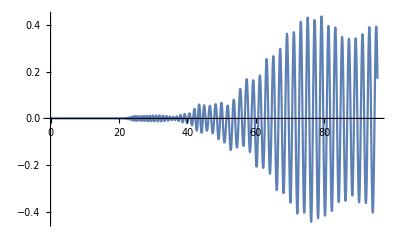

```mathematica
signal=AddSignalRange[data,TotalF->Fs];
ListLinePlot[signal,PlotRange->Full]
```

```mathematica
mag=Abs[Fourier[data]];
```

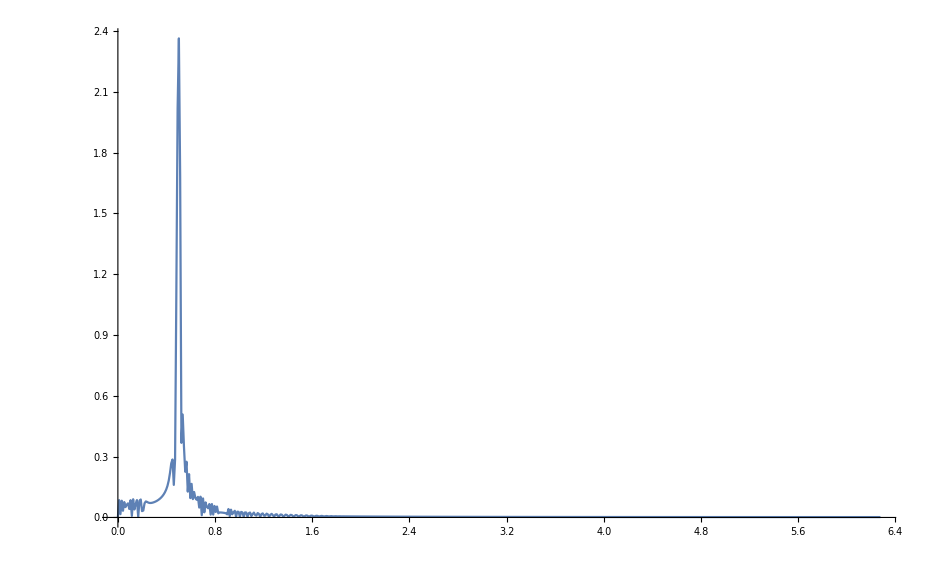

```mathematica
spectrum=AddSpectrumRange[mag,TotalF->Fs,HalfSpectrum->True];
ListLinePlot[spectrum,PlotRange->Full]
```